```mathematica
ClearAll["Global`*"];
NotebookDirectory[];
SetDirectory[NotebookDirectory[]]; (* or else the default directory is Directory[]*)
NotebookDirectory[];
```

# Active SSH

### Parameters

```mathematica
Mms=5.5*^-4*0.5;
Rms=0.34*0.09;
Cmc=1.750252936794995*^-4/0.42 ; (*490*^-6*1.5;*)
omega0 = 1/Sqrt[Mms*Cmc];


sd=12*^-4;(* m^2 diaphragm surface *)
S=0.05*0.05; (*  m^2 duct cross section*)
rho0=1.184;(*[kg/m^3]*)
c0=346;(*%[m/s]*)
a=0.2806;(*[m]*)
kk = -5/Cmc; (*Coupling negative*)
```

### Speaker mechanical impedance

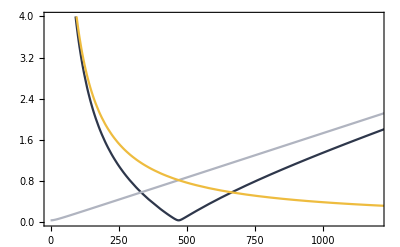

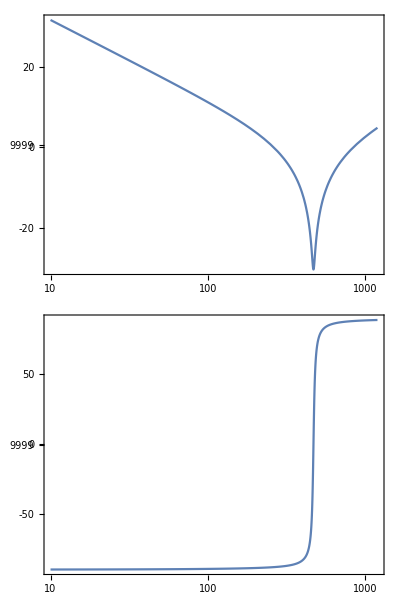

```mathematica
Zms[freq_]:= (I*2*Pi*freq)*Mms + Rms + 1/((I*2*Pi*freq)*Cmc);
ZmsAbv[freq_]:= (I*2*Pi*freq)*Mms + Rms ;
ZmsBlw[freq_]:=  Rms + 1/((I*2*Pi*freq)*Cmc);

Plot[{Abs[Zms[freq] ] ,Abs[ZmsAbv[freq]] ,Abs[ZmsBlw[freq] ]},{freq,0.1,2200},PlotRange->{{0,1200},{0,4}},PlotStyle->{ColorData["GrayYellowTones",0],ColorData["GrayYellowTones",0.5],ColorData["GrayYellowTones",1]},Frame->True]
BodePlot[Zms[f],{f,10,1200}]
```

### Transfer Matrix

True system vs Virtual system

```mathematica
zs[k_] := (ⅈ  k c0)*Mms + Rms + 1/( (ⅈ  k c0)*Cmc);

zr:= rho0 c0 sd/S;

z11[k_] := zs[k]+kk/(ⅈ c0 k);
z12[k_] := -kk/(ⅈ c0 k);
z21[k_] :=z12[k];
z22[k_] :=z11[k];
```

```mathematica
zMat[k_]:=  ({{z11[k], z12[k]}, {z21[k], z22[k]}});

yMat[k_]:=Inverse[zMat[k]];
```

```mathematica
y11[k_]:= Part[yMat[k],1,1];
y12[k_]:= Part[yMat[k],1,2];
y21[k_]:= Part[yMat[k],2,1];
y22[k_]:= Part[yMat[k],2,2];
```

```mathematica
T1[k_] := ({{Exp[-I k a/4], 0}, {0, Exp[+I k a/4]}});

(*T2[k_]:=  zr/(ⅇ^(ⅈ a k/2)(Det[zMat[k]]+2ⅈ z12 [k]zr*Sin[a k/2])) ({{ⅇ^(ⅈ a k/2)(ⅇ^(- ⅈ a k/2)(Det[zMat[k]]/zr-Tr[zMat[k]] )+(z12[k]+z21[k])-zr*2*ⅈ*Sin[k a /2]), ⅇ^((ⅈ a k)/2) (z12[k]+z21[k])-z22[k]+zr-ⅇ^(ⅈ a k) (z11[k]+zr)}, {-ⅇ^((ⅈ a k)/2) (z12[k]+z21[k])+ z11[k]-zr+ⅇ^(ⅈ a k) (z22[k]+zr), ⅇ^(- ⅈ a k/2)(-  ⅇ^(ⅈ a k)( -ⅇ^(ⅈ a k/2) (Det[zMat[k]]/zr+Tr[zMat[k]])+(z12[k]+z21[k])-zr*2*ⅈ*Sin[k a /2]))}});*)

(*T2[k_]:=({{Exp[-ⅈ k a/2], 0}, {0, Exp[ⅈ k a/2]}})+ zr/(-1+2 ⅈ zr y12[k]Sin[(a k)/2])({{ⅇ^((-ⅈ a k)/2)(y11[k]+y22[k]+ⅇ^((-ⅈ a k)/2)y12[k]+ ⅇ^((ⅈ a k)/2)y21[k])+2ⅈ zr Sin[(a k)/2] Det[yMat[k]], ⅇ^((-ⅈ a k)/2)y11[k]+ⅇ^((ⅈ a k)/2)y22[k]+y12[k]+y21[k]+2ⅈ zr Sin[(k a)/2] Det[yMat[k]]}, {-y12[k]-y21[k]-ⅇ^((ⅈ a k)/2)y11[k]-ⅇ^((-ⅈ a k)/2)y22[k]-2 ⅈ zr Sin[(a k)/2]Det[yMat[k]], -(ⅇ^((ⅈ a k)/2) (y11[k]+y22[k]+ⅇ^((ⅈ a k)/2)y12[k]+ⅇ^((-ⅈ a k)/2)y21[k])+2ⅈ zr Sin[(a k)/2]Det[yMat[k]])}});*)

(*T2[k_]:=(- zr ⅇ^(-ⅈ a k))/Det[zMat[k]] ({{-z12[k] -ⅇ^(ⅈ a k) z21[k] +ⅇ^((ⅈ a k)/2) (-Det[zMat[k]]/ zr+Tr[zMat[k]] ), -(z12[k]+ⅇ^(ⅈ a k) z21[k]-ⅇ^((ⅈ a k)/2) Tr[zMat[k]])}, {z12[k]+ⅇ^(ⅈ a k) z21[k]-ⅇ^((ⅈ a k)/2) Tr[zMat[k]], z12[k] +ⅇ^(ⅈ a k) z21[k]+ⅇ^((ⅈ a k)/2) (-Det[zMat[k]]/ zr-Tr[zMat[k]] )}});*)
(*T2[k_]:=({{(ⅇ^((ⅈ a k)/2) (ⅈ kk (sd zr-2 zs[k])+c0 k zs[k] (-sd zr+zs[k])+ⅈ kk sd zr Cos[(a k)/2]))/(zs[k] (-2 ⅈ kk+c0 k zs[k])), -(ⅇ^((ⅈ a k)/2) sd zr (kk+ⅈ c0 k zs[k]+kk Cos[(a k)/2]))/(zs[k] (2 kk+ⅈ c0 k zs[k]))}, {(ⅇ^((ⅈ a k)/2) sd zr (kk+ⅈ c0 k zs[k]+kk Cos[(a k)/2]))/(zs[k] (2 kk+ⅈ c0 k zs[k])), (ⅇ^((ⅈ a k)/2) (c0 k zs[k] (sd zr+zs[k])-ⅈ kk (sd zr+2 zs[k])-ⅈ kk sd zr Cos[(a k)/2]))/(zs[k](-2 ⅈ kk+c0 k zs[k]))}});*)
T2[k_]:=({{(((1+ⅇ^((ⅈ a k)/2)) sd zr-2 zs[k]) (4 kk+ⅈ c0 k ((-1+ⅇ^((ⅈ a k)/2)) sd zr+2 zs[k])))/(-2 kk sd zr+2 ⅇ^(ⅈ a k) kk sd zr-4 ⅇ^((ⅈ a k)/2) zs[k] (2 kk+ⅈ c0 k zs[k])), -(ⅈ sd zr (2 kk+2 (kk+ⅈ c0 k zs[k]) Cos[(a k)/2]-c0 k sd zr Sin[(a k)/2]))/(4 ⅈ kk zs[k]-2 c0 k zs[k]^2+2 kk sd zr Sin[(a k)/2])}, {(ⅈ sd zr (2 kk+2 (kk+ⅈ c0 k zs[k]) Cos[(a k)/2]-c0 k sd zr Sin[(a k)/2]))/(4 ⅈ kk zs[k]-2 c0 k zs[k]^2+2 kk sd zr Sin[(a k)/2]), (-4 ⅇ^((ⅈ a k)/2) kk sd zr+ⅈ c0 k sd^2 zr^2-ⅈ ⅇ^(ⅈ a k) (sd zr+2 zs[k]) (-4 ⅈ kk+c0 k (sd zr+2 zs[k])))/(-2 kk sd zr+2 ⅇ^(ⅈ a k) kk sd zr-4 ⅇ^((ⅈ a k)/2) zs[k] (2 kk+ⅈ c0 k zs[k]))}});

Ttot[k_]:= T1[k].T2[k].T1[k] //FullSimplify;

M11[k_]:= Part[Ttot[k],1,1];
M12[k_]:= Part[Ttot[k],1,2];
M21[k_]:= Part[Ttot[k],2,1];
M22[k_]:= Part[Ttot[k],2,2];


M[k_]:= {{M11[k],M12[k]},{M21[k],M22[k]}}//FullSimplify ;
(*ReImPlot[M[2*Pi*freq/c0].M[2*Pi*freq/c0],{freq,10,1200},PlotRange->{{0,1200},{-1,1}},Frame->True]*)
MatrixForm[M[k]];
```

### Scattering Matrix

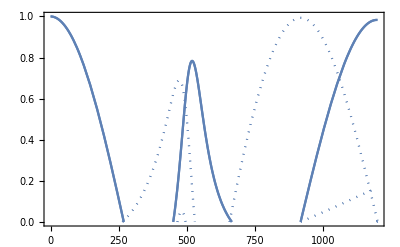

```mathematica
SS[k_]:= {{-M21[k]/M22[k],1/M22[k]},{M11[k]-M12[k]*M21[k]/M22[k],M12[k]/M22[k]}};

(*MatrixForm[SS[k]]//FullSimplify*)


ReImPlot[SS[2*Pi*freq/c0],{freq,0.1,1200},PlotRange->{{0,1200},{0,1}},Frame->True];
```

### Dispersion

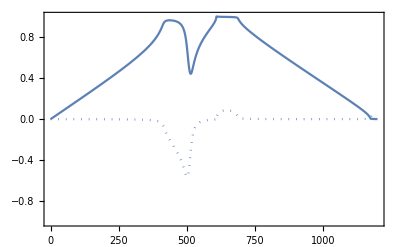

```mathematica
TrFunc[k_]:= Tr[M[k]]/2 ;
(*TrFunc[k_]:= Tr[M[k]]- Sqrt[Tr[M[k]]^2-4*Det[Tr[M[k]]]];*)
(*TraceM1[k_]:= (M11[k]+ M22[k])/2- Sqrt[((M11[k]+ M22[k])/2)^2+M12[k]+ M21[k]];*)

q[k_] :=ArcCos[ TrFunc[k]]/a;
q[k]//FullSimplify;
FullSimplify[%];
(*ToMatlab[%];*)
ReImPlot[q[2*Pi*freq/c0]*a/Pi,{freq,0.1,1200},PlotRange->{{0,1200},{-1,1}},Frame->True]
```

### Energy conserving = S-matrix is unitary

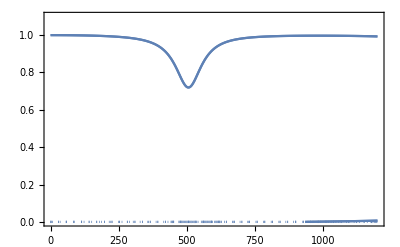

```mathematica
ReImPlot[SS[2*Pi*freq/c0].Transpose[Conjugate[SS[2*Pi*freq/c0]]],{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}},Frame->True]
```

### SU (1, 1) group?

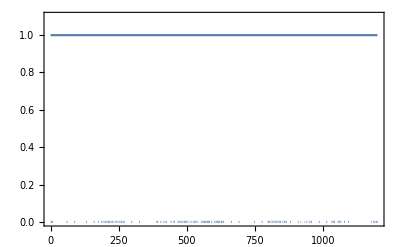

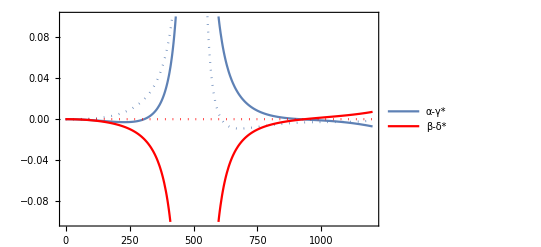

```mathematica
ReImPlot[M11[2*Pi*freq/c0]*M22[2*Pi*freq/c0] - M12[2*Pi*freq/c0]*M21[2*Pi*freq/c0] ,{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}},Frame->True]
p1 = ReImPlot[M11[2*Pi*freq/c0]-Conjugate[M22[2*Pi*freq/c0]]  ,{freq,0.1,1200},PlotRange->{{0,1200},{-0.1,0.1}},Frame->True,PlotLegends->LineLegend[{"α-γ*"}]];
p2 = ReImPlot[M12[2*Pi*freq/c0]-Conjugate[M21[2*Pi*freq/c0]]  ,{freq,0.1,1200},PlotRange->{{0,1200},{-0.1,0.1}},Frame->True,PlotLegends->LineLegend[{"β-δ*"}],PlotStyle->Red];
Show[p1,p2, PlotRange->All]

(*ReImPlot[MatrixPower[M[2*Pi*freq/c0],2],{freq,0.1,1200},PlotRange->{{0,1200},{-2,2}},Frame->True]*)
```

### Topology

```mathematica
AlphaR[k_]:= Re[M11[k]]
AlphaI[k_]:=Im[M11[k]]
BetaR[k_]:=Re[M21[k]]
BetaI[k_]:=Im[M21[k]]

coneplot = Plot3D[{Sqrt[x^2+y^2],-Sqrt[x^2+y^2]},{x,-2,2},{y,-2,2},
RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic,
ColorFunction->"RustTones",
PlotStyle->Opacity[0.5],
Mesh-> False,
Boxed->False,
Axes->False,
AxesOrigin->{0,0,0},
AxesStyle->Opacity[1],
TicksStyle->None,
AxesLabel->{Style[hi,16],Style[y,16],Style[z,16]},
ViewPoint->{Pi,Pi/2,2},Background->None]
Export["cone.png",coneplot,Background->None,ImageResolution-> 300]

Directory[]
```

-Graphics3D-

cone.png

C:\Users\padlewsk\Documents (Local)\projects\SSH\mathiematica

### Mapping to spring/mass model

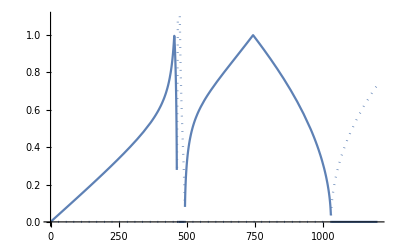

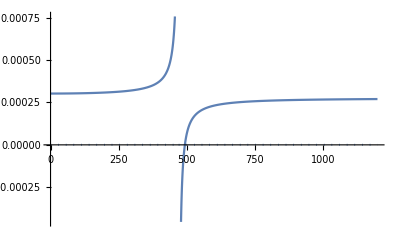

```mathematica
k1 =2800;
k2 =2800;


Meff[omega_]:= Mms*( 1+0.1*omega0^2/(omega0^2-omega^2));
q2[omega_]:=ArcCos[1-(Meff[omega]*omega^2)*(2*k1 + 2*k2 - (Meff[omega]*omega^2))/(2*k1*k2)]/a;
FullSimplify[%]
q2[omega];
ReImPlot[q2[omega]*a/Pi,{omega,0,1000}];
ReImPlot[q2[2*Pi*freq]*a/Pi,{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}}]
ReImPlot[Meff[2*Pi*freq],{freq,0,1200}]
FullSimplify[%];
```

### Test...

```mathematica
f[x_]:= Exp[I*2*Pi*freq/c0*a/8]
```

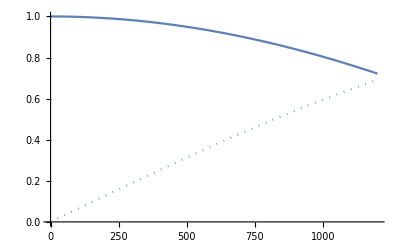

```mathematica
ReImPlot[f[freq],{freq,0,1200}]
```